## Define Potential & Solve for Cosmological Parameters

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.847412}

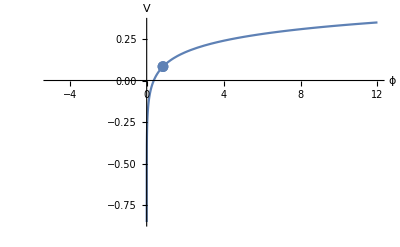

vacuumArray = {}

ϕ0 = 0.847412

f[t] = ConditionalExpression[-0.359053+0.5 t^2+1. (0.238975+0.5 t^2 (-0.5+1. Log[t])),(1.08047×10^-16<t<0.847412&&((t∈Reals&&Re[1/(-0.847412+t)]<-1.18006)||(Re[1/(-0.847412+t)]≤-1.18006&&(t∉Reals||Re[t]≥0.847412))))||((Re[1/(-0.847412+t)]≤-1.18006||Re[1/(-0.847412+t)]≥0)&&(t∉Reals||Re[t]≥0.847412))||1/(-0.847412+t)∉Reals]

f[0.001] = -0.120082

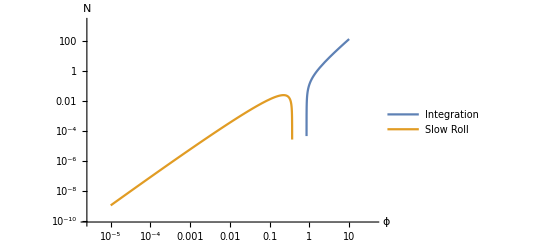

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve ni==f[t] returns: {}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕi1s = {7.90087}

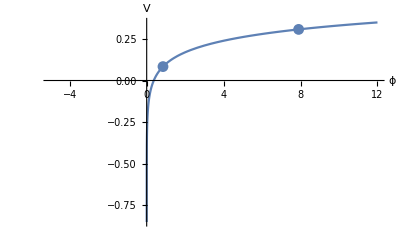

NDSolve::ndsz: At n == -1.40065, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-2.79831} lies outside the range of data in the interpolating function. Extrapolation will be used.

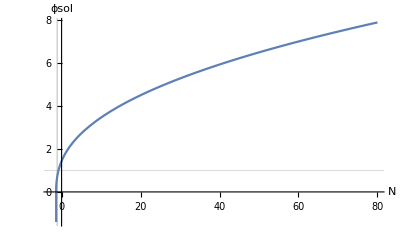

At n = 0, ϵ1 = 0.0985177

InterpolatingFunction::dmval: Input value {-2.79831} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

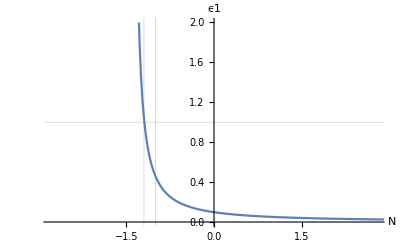

At n1 = -1.19314, ϵ1 = 1.

ϕi2 = 7.85151

ϕpi2 = 0.0415185

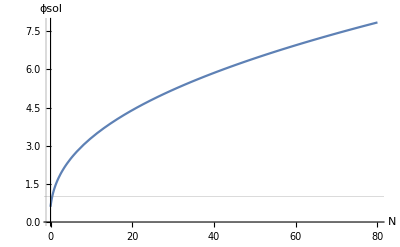

ϕsol2[60] = 6.9541

At n = 0, ϵ1 = 0.999885

ns[60] = 0.978928

r[60] = 0.0190286

```mathematica
(* Define an inflationary potential *)
left = False;
v[x_]:=(0.1)*(1+Log[x]); 
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -2.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.847467}

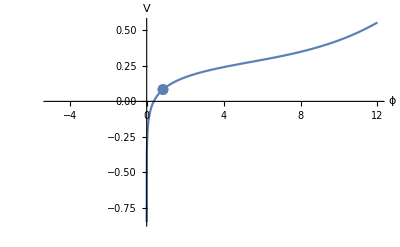

vacuumArray = {}

ϕ0 = 0.847467

$Aborted

ABORTED

```mathematica
(* Define an inflationary potential *)
left = False;
v[x_]:=(0.1)*(1+Log[x]); (* +0.0001*x^4 *)
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -2.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```